```mathematica
ClearAll["Global`*"]
```

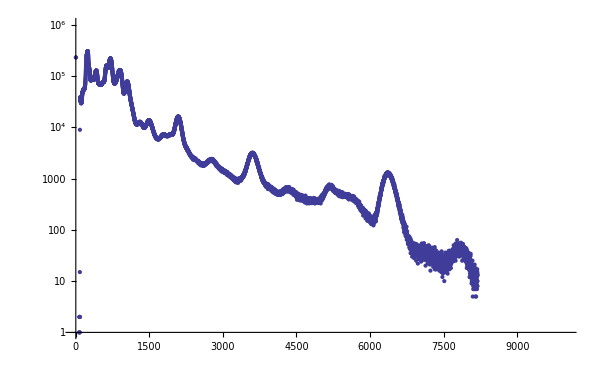

```mathematica
imp=Import[ParentDirectory[NotebookDirectory[]]<>"\\data\\th.TKA","Table"];
data=Transpose[imp][[1]];
data=Table[{i,data[[i]]},{i,1,Length[data]}];
ListLogPlot[data,PlotRange->{{0,10000},{1,10^6}},ImageSize->600]
```

```mathematica
nlm=NonlinearModelFit[data,{
A1 Exp[-1/2((x-x01)/σ1)^2]+
A1b Exp[-1/2((x-x01b)/σ1b)^2]+
A2 Exp[-1/2((x-x02)/σ2)^2]+
A2b Exp[-1/2((x-x02b)/σ2b)^2]+
A3 Exp[-1/2((x-x03)/σ3)^2]+
A3b Exp[-1/2((x-x03b)/σ3b)^2]+
A4 Exp[-1/2((x-x04)/σ4)^2]+
A4b Exp[-1/2((x-x04b)/σ4b)^2]+
A5 Exp[-1/2((x-x05)/σ5)^2]+
u1+u2 x},{
{A1,120000},{x01,572},{σ1,400},
{A1b,7000},{x01b,1500},{σ1b,50},
{A2,10000},{x02,2003},{σ2,100},
{A2b,300},{x02b,2770},{σ2b,50},
{A3,2000},{x03,3600},{σ3,100},
{A3b,100},{x03b,4300},{σ3b,100},
{A4,300},{x04,5160},{σ4,100},
{A4b,300},{x04b,5610},{σ4b,100},
{A5,1000},{x05,6380},{σ5,100},
{u1,-10000},{u2,-1}},x]
nlm["ParameterTable"]
```

FittedModel[-241787.+«9»+18.947 x]

| Estimate | Standard Error | t-Statistic | P-Value
A1 | 356506. | 1.00657×10^6 | 0.354179 | 0.723214
x01 | 539.726 | 230.833 | 2.33817 | 0.0194024
σ1 | 695.886 | 464.946 | 1.4967 | 0.134509
A1b | 40969.6 | 26076.9 | 1.5711 | 0.116197
x01b | 1528.53 | 24.899 | 61.3893 | 2.2832302958×10^-675
σ1b | 149.039 | 32.2025 | 4.62818 | 3.74594×10^-6
A2 | 88764.7 | 214472. | 0.413875 | 0.678976
x02 | 1913.48 | 118.415 | 16.1591 | 7.69417×10^-58
σ2 | 272.252 | 169.726 | 1.60407 | 0.108738
A2b | 85180.4 | 765673. | 0.111249 | 0.911422
x02b | 2396.15 | 482.973 | 4.96126 | 7.14522×10^-7
σ2b | 394.853 | 953.167 | 0.414254 | 0.678699
A3 | 73821.8 | 1.98578×10^6 | 0.0371752 | 0.970346
x03 | 3016.01 | 2773.83 | 1.08731 | 0.276934
σ3 | 587.138 | 4182.07 | 0.140394 | 0.888352
A3b | 58953.1 | 8.71978×10^6 | 0.00676085 | 0.994606
x03b | 3816.96 | 29771.3 | 0.12821 | 0.897986
σ3b | 876.723 | 27475.7 | 0.031909 | 0.974545
A4 | 70285.1 | 1.68411×10^7 | 0.00417343 | 0.99667
x04 | 4917.18 | 129789. | 0.0378859 | 0.96978
σ4 | 1439.18 | 125115. | 0.0115028 | 0.990823
A4b | 85601.8 | 4.52905×10^6 | 0.0189006 | 0.984921
x04b | 7409.43 | 332240. | 0.0223014 | 0.982208
σ4b | 2484.7 | 134880. | 0.0184215 | 0.985303
A5 | 878.777 | 2246.61 | 0.391156 | 0.695692
x05 | 6374.3 | 210.953 | 30.2168 | 3.18094×10^-190
σ5 | 80.4519 | 258.813 | 0.310849 | 0.755923
u1 | -241787. | 616875. | -0.391954 | 0.695102
u2 | 18.947 | 643.5 | 0.0294437 | 0.976511

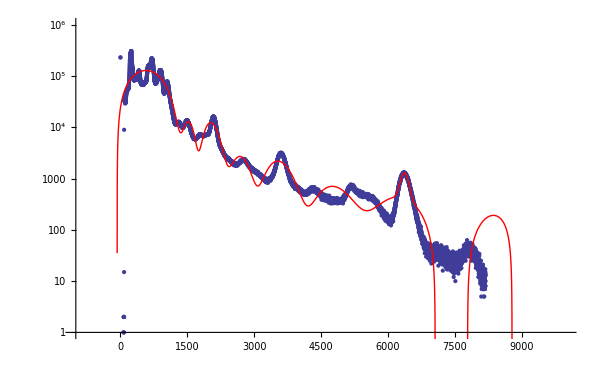

```mathematica
Show[ListLogPlot[data,PlotRange->{{-1000,10000},{1,10^6}},ImageSize->600],LogPlot[Normal[nlm],{x,-1000,10000},PlotStyle->Red]]
```

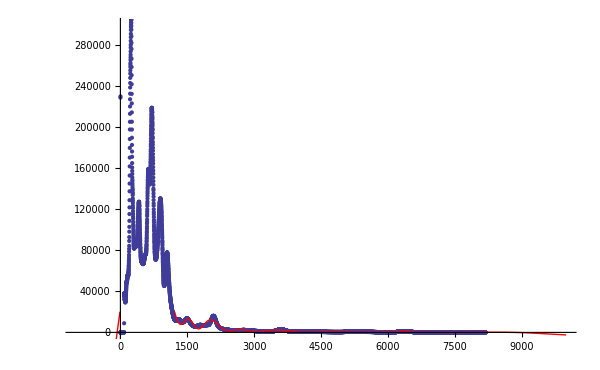

```mathematica
Show[ListPlot[data,PlotRange->{{-1000,10000},{0,300000}},ImageSize->600],Plot[Normal[nlm],{x,-1000,10000},PlotStyle->Red]]
```